```mathematica
(* Kwiatkowski,D.& Nowak,M.(1991) Periodic and chaotic host-parasite interactions in human malaria Proceedings of the National Academy of Sciences of the United States of America 88,5111-5113. *)
```

```mathematica
(*model 1.6 Kwiatkowski and Nowak 2 stages*)
DominicNowak1[initxy_List,lsd_List,r_,lsPS_List,runT_,outform_]:=Module[{d1,d2,i,outtemp,tot,Fx,p,s,x0,y0,xold,yold,xnew,ynew},outtemp={};
p=lsPS[[1]];s=lsPS[[2]];
x0=initxy[[1]];y0=initxy[[2]];
d1=lsd[[1]];d2=lsd[[2]];
tot=x0+y0;
Fx=36.5+4(1-Exp[-0.0003*x0]);
i=0;
xold=x0;yold=y0;
AppendTo[outtemp,{i,x0,y0,tot,Fx}];
While[i≤runT,i=i+1;
ynew=d1*xold*Exp[-p*xold];
xnew=r*d2*yold*Exp[-s*xold];
Fx=36.5+4*(1-Exp[-0.0003*xnew]);
tot=xnew+ynew;
AppendTo[outtemp,{i,xnew,ynew,tot,Fx}];
xold=xnew;yold=ynew;];
If[outform==0,outtemp]
];

Manipulate[
lsout=DominicNowak1[{x0,y0},{d1,d2},r,{p,s},maxt,0];
npara=Table[{i,Log10@lsout[[i,4]]},{i,1,Length@lsout}];
temp=Table[{i,lsout[[i,5]]},{i,1,Length@lsout}];
GraphicsColumn[{
ListPlot[npara,Frame->{True,True,False,False},FrameLabel->{"time (days)","log10 number of parasites"},PlotRange->{0,6},Joined->True],

ListPlot[temp,Frame->{True,True,False,False},Joined->True,FrameLabel->{"time (days)","F(x)"},PlotRange->{35,42}]}],
Style["Mahidol-Oxford Tropical Medicine Research Unit",Bold],Delimiter,
Style["Kwiatkowski,D.& Nowak,M. PNAS (1991)"]
,
Delimiter,
{{x0,1},1,10,1,Appearance->"Labeled"},
{{y0,1},1,10,1,Appearance->"Labeled"},
Delimiter,
{{d1,1},0,1,Appearance->"Labeled"},
{{d2,1},0,1,Appearance->"Labeled"},
Delimiter,
{{r,4},0,20,Appearance->"Labeled"},
{{p,0.0002},0.00001,0.1,Appearance->"Labeled"},
{{s,0.001},0.0,0.1,Appearance->"Labeled"},
{{maxt,50,"max time"},1,100,1,Appearance->"Labeled"}
,SaveDefinitions->True
]
```

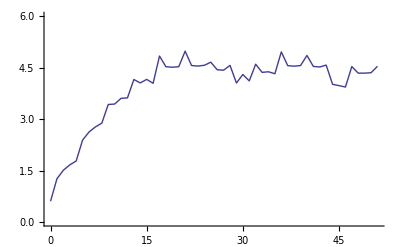

```mathematica
lsout=DominicNowak[{1,1,1,1},16,16,0.05,{1,1,1,1},{0.00001,0.00002,0.0001,0.001},50];
ls=Table[{lsout[[i,1]],Log10@lsout[[i,3]]},{i,1,Length@lsout}];
ListPlot[ls,Joined->True,PlotRange->{0,6}]
```

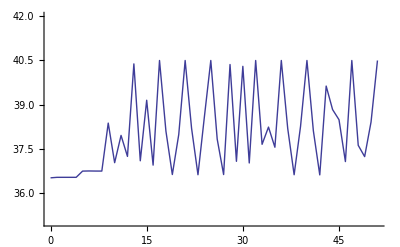

```mathematica
ls2=Table[{lsout[[i,1]],lsout[[i,4]]},{i,1,Length@lsout}];
ListPlot[ls2,Joined->True,PlotRange->{35,42}]
```